### Emaad Khwaja - Optical Materials And Device - Problem Set #1

## Problem 1. Perfect Lens One of the most surprising claims of Veselago and Pendry is that waves experience a negative phase delay inside of such media and evanescent waves get exponentially amplified.As we will see, some of these intriguing optical properties are already evident from the transmission properties.

### a) Derive the formula of the total amplitude transmission t of a plane wave incident from the left side on a slab with optical properties ε_2, μ_2 and thickness d, surrounded by a material with ε_2 and μ_2 and express it in terms of the transmission and reflection coefficients of the two interfaces of the slab. Hint 1 : Consider all light paths contributing to the total transmission, including multiple reflected waves inside of the slab. Hint 2 : Use the infinite geometric series formula : ∑_(n=0)^∞ p^n=1/(1-p)

If light is s-polarized,the electric field:

	E_(0S+)=[0,1,0]e^(ik_(z,1)z+ik_1-iωt)

where,  
	k_1=ω/c √(ϵ_1 μ_1),        ϵ_1 μ_1 ω^2/c^2<k_1^2+(k_(||))^2
	k_(z,1)= √(kx_1^2+ky_1^2-(k_(||))^2)

at the interface between the material 1 and the slab 2, reflection occurs. Therefore:
E_(0S-)=r_21[0,1,0]e^(-ik_(z,1)z+ik_1-iωt)
as well as transmission given by,
	E_(1S+)=t_12[0,1,0]e^(ik_(z,2)z+ik_2-iωt),
where  ,
	k_2=ω/c √(ϵ_2 μ_2),      ϵ_2 μ_2 ω^2/c^2<k_1^2+(k_(||))^2
	k_(z,2)= √(kx_2^2+ky_2^2-(k_(||))^2)
Since the wave front must be continuous across the mediums, it follows that at the initial interface:
t_12=(2 μ_2 k_(z,1))/(μ_2 k_(z,1) + μ_1 k_(z,2))√((ϵ_1×μ_2)/(ϵ_2×μ_1)),            r_21 = (μ_2 k_(z,1) - μ_1 k_(z,2))/(μ_2 k_(z,1) +  μ_1 k_(z,2))
and within the medium:
t_23=(2 μ_1 k_(z,2))/(μ_1 k_(z,2) + μ_2 k_(z,1))√((ϵ_2×μ_1)/(ϵ_1×μ_2)),            r_23 = (μ_1 k_(z,2) - μ_2 k_(z,1))/(μ_1 k_(z,2) + μ_2 k_(z,1))

Transmission is then obtained by adding the scattering events across both interfaces:
t=t_12 t_23 e^(ik_(z,2)d)+ t_12 t_23 r_21 r_23 e^(3 ik_(z,2)d) + t_12(t_23(r_21 r_23))^2 e^(5 ik_(z,2)d)+... = t_12 t_23 e^(ik_(z,2)d)∑_(n=0)^∞ (r_21 r_23 e^(2 ik_(z,2)d))^n
Evaluating this infinite geometric sum via ∑_(n=0)^∞ p^n=1/(1-p):
t_s=(t_12 t_23 e^(ik_(z,2)d))/(1 - r_21 r_23 e^(2 ik_(z,2)d))

If the light is p-polarized, then:
t_12=(2 ϵ_2 k_(z,1))/(ϵ_2 k_(z,1) + ϵ_1 k_(z,2))√((ϵ_1×μ_2)/(ϵ_2×μ_1)),            r_21 = (ϵ_2 k_(z,1) - ϵ_1 k_(z,2))/(ϵ_2 k_(z,1) +  ϵ_1 k_(z,2)),
	t_23=(2 ϵ_1 k_(z,2))/(ϵ_1 k_(z,2) + μ_2 k_(z,1))√((ϵ_2×μ_1)/(ϵ_1×μ_2)),            r_23 = (ϵ_1 k_(z,2) - ϵ_2 k_(z,1))/(ϵ_1 k_(z,2) + ϵ_2 k_(z,1))
	t_p= (t_12 t_23 e^(ik_(z,2)d))/(1 - r_21 r_23 e^(2 ik_(z,2)d))

### b) Consider a dielectric slab (a so - called' etalon') with d = 400 nm, ε_2 = 10 and μ_2 = 1 surrounded by air.Apply the derived formula to plot the intensity transmission through this slab as a function of frequency ω in the visible regime.Assume p - polarized light, which is incident at θ = 0 in the x - z plane (k_(y,1) = 0).What do you see?What is the physical origin of the fluctuations?

```mathematica
Subscript[ϵ, 0]=1;
Subscript[μ, 0]=1;

Subscript[ϵ, 2]= 10×Subscript[ϵ, 0];
Subscript[μ, 2]=1×Subscript[μ, 0];
d=400*10^-9;
c=299792458 (*speed of light (m/s)*);
Subscript[ϵ, 1]=1.0006×Subscript[ϵ, 0] (*air permittivity*);
Subscript[μ, 1]=1.00000037×Subscript[μ, 0] (*air permeability*);
k=0; (*parallel k component*) 

Subscript[k, 1][ω_]:=ω/c √(Subscript[ϵ, 1]×Subscript[μ, 1]);
Subscript[k, 2][ω_]:=ω/c √(Subscript[ϵ, 2]×Subscript[μ, 2]);
Subscript[k, z1][ω_]:=√((Subscript[k, 1][ω])^2-k^2);
Subscript[k, z2][ω_]:=√((Subscript[k, 2][ω])^2-k^2);
Subscript[t, 12][ω_]:=(2×Subscript[ϵ, 2]×Subscript[k, z1][ω])/(Subscript[ϵ, 2]×Subscript[k, z1][ω]+Subscript[ϵ, 1]×Subscript[k, z2][ω])√((Subscript[ϵ, 1]×Subscript[μ, 2])/(Subscript[ϵ, 2]×Subscript[μ, 1]));
Subscript[t, 23][ω_]:=(2×Subscript[ϵ, 1]×Subscript[k, z2][ω])/(Subscript[ϵ, 1]×Subscript[k, z2][ω]+Subscript[ϵ, 2]×Subscript[k, z1][ω])√((Subscript[ϵ, 2]×Subscript[μ, 1])/(Subscript[ϵ, 1]×Subscript[μ, 2]));
Subscript[r, 21][ω_]:=(Subscript[ϵ, 2]×Subscript[k, z1][ω]-Subscript[ϵ, 1]×Subscript[k, z2][ω])/(Subscript[ϵ, 2]×Subscript[k, z1][ω]+Subscript[ϵ, 1]×Subscript[k, z2][ω]);
Subscript[r, 23][ω_]:=(Subscript[ϵ, 1]×Subscript[k, z2][ω]-Subscript[ϵ, 2]×Subscript[k, z1][ω])/(Subscript[ϵ, 1]×Subscript[k, z2][ω]+Subscript[ϵ, 2]×Subscript[k, z1][ω]);
T[ω_]:=(Subscript[t, 12][ω]×Subscript[t, 23][ω]×E^(I×d×Subscript[k, z2][ω]))/(1-Subscript[r, 21][ω]×Subscript[r, 23][ω]×E^(2×I×d×Subscript[k, z2][ω]));


Plot[{Abs[Re[T[ω]]],Arg[T[ω]]/π},{ω,2*Pi*4*10^14,2*Pi*7.5*10^14}
,PlotRange->All, PlotLegends->{"Real Component","Arg (t)"}
,PlotLabel->Style["Total Amplitude Transmission of 400nm Air
Etalon",Bold,Black],AxesStyle->Medium,Frame->{True,True,
False,True},FrameLabel->{{Style["t_p Transmission Coefficient
",RGBColor[0.368417, 0.506779, 0.709798]],Style["Phase (π)",
RGBColor[0.880722, 0.611041, 0.142051]]},{Style["ω Angular 
Frequency (rad/s)",Black],None}},Epilog->{Directive[RGBColor
[0.880722, 0.611041, 0.142051]],Line[{{3.724*10^15,-1},
{3.724*10^15,1}}]}]
```

-Graphics-

It is clear that fluctuations occur across the visible range, and the phase shifts over 2π, within the etalon. Constructive interference occurs if the transmitted beams (k_1 and k_2) are in phase, and this corresponds to a high transmission (peak) in the etalon. If the transmitted beams are out of phase, destructive interference occurs and this corresponds to a transmission minimum. This is indicated by the half values of the Arg(t) near the minimums.

### c) Use the same equation as in b) to plot the intensity transmission and arg (t) as a function of the normalized parallel wavevector in the interval 0 ≤ k_(||) = k_1 ≤ 2 at ω = 2 π ×375 THz.Assume that all materials are air (ε_1 = ε_2 = 1 and μ_1 = μ_2 = 1) and d = 50 nm.What do you see?What does k_(||) > 1 mean for the incidence angle and kz?What is the physical significance of arg (t)?

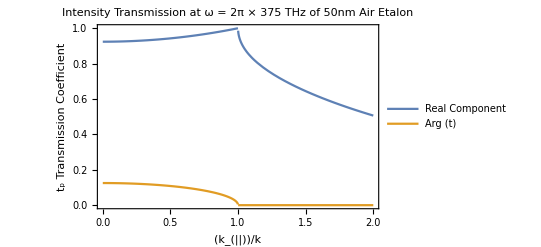

```mathematica
Subscript[ϵ, 2]= 1 ×Subscript[ϵ, 0];
Subscript[μ, 2]=1 ×Subscript[μ, 0];
d=50*10^-9;
ω=2*Pi*3.75*10^14;

Subscript[k, 1]=ω/c √(Subscript[ϵ, 1]×Subscript[μ, 1]);
Subscript[k, 2]=ω/c √(Subscript[ϵ, 2]×Subscript[μ, 2]);
Subscript[k, z1][K_]:=√((Subscript[k, 1])^2-(K*Subscript[k, 1])^2);
Subscript[k, z2][K_]:=√((Subscript[k, 2])^2-(K*Subscript[k, 2])^2)

(*Here K represents the ratio of the parallel vector to the incident one*)

Plot[{Abs[Re[T[K]]],Arg[T[K]]/π},{K,0,2},PlotRange->All,
PlotLegends->{"Real Component","Arg (t)"},
PlotLabel->Style["Intensity Transmission at ω = 2π × 375 THz
\n of 50nm Air Etalon",Bold,Black],AxesStyle->Medium,Frame->
{True,True,False,True},FrameLabel->{{Style["t_p Transmission 
Coefficient",RGBColor[0.368417, 0.506779, 0.709798]],
Style["Phase (π)",RGBColor[0.880722, 0.611041, 0.142051]]},
{Style["(k_(||))/k",Black],None}}]
```

There is a discontinuity at k_(||)=1. This means that k_1 is now perpendicular to the surface, so the angle of incidence is 0 degrees.At k_(||)>1, the angle of incidence (Sin^-1(k_(||))/k_1) is complex and k_z is a complex value with no real component. Therefore, k_1 propagates parallel to the boundary and has a decaying transmission amplitude perpendicular to the boundary. This means k_z is externally reflecting.The transmission amplitude decays exponentially. This indicates that at these k values, the transmitted waves are evanescent. Arg (t) represents the phase of the transmitted waves, and Arg (t) = 0 represents an external reflection because it indicates there is no phase within the medium.

### d) Describe qualitatively how the amplitude of propagating ( ω^2/c^2 > (k_(||))^2 ) and evanescent (ω^2/c^2 < (k_(||))^2) waves changes as a function of distance if the slab is made of air. And what happens in the case of negative index metamaterial (ε_2 = -1 and μ_2 = -1)? What are the directions of k_(z,2), Poynting vector, phase advancement and energy flux in the negative index metamaterial?

In ideal materials, the amplitude of propagating waves is constant regardless of the distance from the slab. This is identical for both the air slab and the negative index material, with the only difference being the negative index material is 180 degrees out of phase with respect to the air slab, as indicated by the negated values in the Arg(t) of their respective transmission plots. 

-Graphics-
In both cases, the amplitude evanescent field decays exponentially. In the air slab, this decay occurs very quickly and transmission terminates in the near-field. 

However, since the evanescent vector grows significantly within the negative index metamaterial, the decay is much slower and the transmission is able to reach the far-field.

In the air slab:
- k_2 points in the forward (positive) direction
- k_(z,2)points in the positive direction
- The Poynting vector points in the positive direction, in the same direction of the wave vector k_2.
-The phase advancement is in the positive direction.
-The energy flux direction is in the positive direction, given by the Poynting vector.

 In the negative index material: 
- k_2 points in the same forward direction
- k_(z,2)points in the negative direction
- The Poynting vector points in the negative direction, opposite the direction of the wave vector k_2.
-The phase advancement is in the opposite direction such that the air slab and the negative index metamaterial are 180 degrees out of phase with one another.
-The energy flux direction is in the negative direction, given by the Poynting vector.

### e) Make the same plots as in c) at ω = 2 π ×375 THz for a slab of metamaterial with ε_2 = -1 and μ_2 = -1 and d = 50 nm. Pay attention to the orientation of k_(z,2). What is the surprising part about these plots as compared to c)?

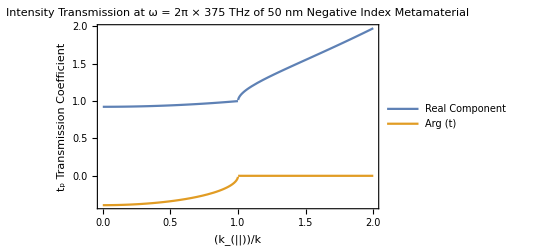

```mathematica
Off[Power::infy]
Off[Infinity::indet]
Subscript[ϵ, 2]= -1 × Subscript[ϵ, 0];
Subscript[μ, 2]= -1 × Subscript[μ, 0];

Subscript[k, 2]=-ω/c √(Subscript[ϵ, 2]×Subscript[μ, 2]);
Subscript[k, z2][K_]:=-√((Subscript[k, 2])^2-(K*Subscript[k, 2])^2);


Plot[{Abs[Re[T[K]]],Arg[T[K]]},{K,0,2},PlotRange->All, 
PlotLegends->{"Real Component","Arg (t)"},PlotLabel->
Style["Intensity Transmission at ω = 2π × 375 THz \n 
of 50 nm  Negative Index Metamaterial",Bold,Black],
AxesStyle->Medium,Frame->{True,True,False,True},
FrameLabel->{{Style["t_p Transmission Coefficient",
RGBColor[0.368417, 0.506779, 0.709798]],
Style["Phase (π)",RGBColor[0.880722, 0.611041, 0.142051]]},
{Style["(k_(||))/k",Black],None}}]
```

There is an increase in propagation when k_(||) > 1. This indicates the ability of the metamaterial to transmit the evanescent waves.

## Problem 2. Hyperbolic metamaterials

#### Type I and Type II hyperbolic metamaterials can be constructed with array of metal nanowires/thin film.The permittivity tensors can be calculated using the Maxwell-Garnett approximation:where f is the volume fraction of the metal inclusions,εh is the permittivity of the host and εi is that of the inclusion.εMG is the effective permittivity tensor and p=x,y or z.Here the numbers νp (0<νp<1,νx+νy+νz=1) are the ellipsoid depolarization factors.For spheres,we have νp=1∕3 for all p.For prolate spheroids resembling long,thin needles,we have νx=νy→1∕2 and νz→0. For oblate spheroids resembling thin films,νx=νy→0 and νz→1 Please consider the silver inclusions in aluminum oxide host in 2 forms:nanowire array and stack of thin films.Use realistic geometric parameters (hint:refer to a published paper) to plot the permittivity components in the wavelength range from 0.3um to 1.2um.Label the frequency range where hyperbolic behavior can be achieved.Include the code you use to plot the curves.

For silver nanowires in aluminum oxide host, a metal volume fraction of .2 was obtained from:

Yao, J., Wang, Y., Tsai, K.-T., Liu, Z., Yin, X., Bartal, G., Zhang, X. (2011). Design, fabrication and characterization of indefinite metamaterials of nanowires. Philosophical Transactions of the Royal Society A: Mathematical, Physical and Engineering Sciences, 369(1950), 3434–3446. doi: 10.1098/rsta.2011.0159

Nanowires were treated as prolate spheroids with ν_xy=ν_y→1∕2 and ν_z→0

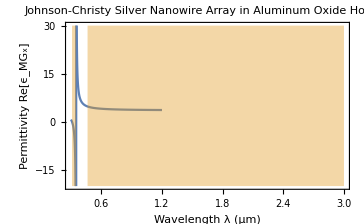

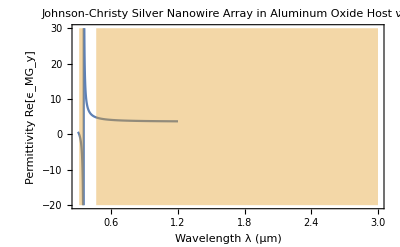

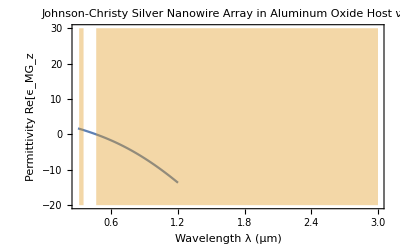

```mathematica
Subscript[v, x]=1/2;
Subscript[v, y]=1/2;
Subscript[v, z]=0;
f=.2;

Silver=Import["/Users/emaad/Downloads/Silver.csv","Dataset","HeaderLines"->1];

list={};

For[i=1,i<=Length[Silver],i++,
λ=Silver[i][1];
Subscript[ϵ, 2]=(Silver[i][2]+Sqrt[-1]*Silver[i][3])^2;
AppendTo[list,{λ,Re[Subscript[ϵ, 2]]}];]

(*Epsilon Interpolation Function*)
SmoothingSplineFunction[dat_?MatrixQ,p:(_?NumericQ|Automatic):Automatic]:=Module[{n=Length[dat],pv=p,cc,dc,del,h,qg,qm,rh,tm,uv,xa,ya},{xa,ya}=Transpose[dat];h=Differences[xa];rh=1/h;
del=Differences[ya] rh;
qm=SparseArray[{Band[{1,1}]->Most[rh],Band[{1,2}]->-ListCorrelate[{1,1},rh],Band[{1,3}]->Rest[rh]},{n-2,n}];
tm=SparseArray[{Band[{2,1}]->Most[Rest[h]],Band[{1,1}]->ListCorrelate[{2,2},h],Band[{1,2}]->Drop[h,-2]},{n-2,n-2}];
qg=qm.Transpose[qm];
If[pv===Automatic,pv=1/(1+Tr[tm]/(6 Tr[qg]))];
uv=LinearSolve[6 (1-pv) qg+pv tm,Differences[del]];
dc=ya-6 (1-pv) Differences[ArrayPad[Differences[ArrayPad[uv,1]]/h,1]];
Interpolation[Transpose[{List/@xa,dc,Append[Differences[dc]/h-h ListCorrelate[{2,1},ArrayPad[pv uv,1]],pv Last[uv] Last[h]-(Subtract@@Take[dc,-2])/Last[h]]}],InterpolationOrder->1,Method->"Hermite"]]
smth=SmoothingSplineFunction[list,9/10];

Subscript[ϵ, i][λ_]:=smth[λ];

Subscript[ϵ, h]=2.4;

Subscript[ϵ, MG][v_,λ_]:= Subscript[ϵ, h](1+(1-v)×f×(Subscript[ϵ, i][λ]-Subscript[ϵ, h])/(Subscript[ϵ, h]+v×(Subscript[ϵ, i][λ]-Subscript[ϵ, h])))/(1-v×f×(Subscript[ϵ, i][λ]-Subscript[ϵ, h])/(Subscript[ϵ, h]+v×(Subscript[ϵ, i][λ]-Subscript[ϵ, h])));



p0= λ/.Select[Solve[Subscript[ϵ, MG][Subscript[v, x],λ]==0,λ],Element[λ/.#1,Reals]&];
(*vertical asymptote*)

TypeI=Graphics[{Opacity[.4],
RGBColor[0.880722, 0.611041, 0.142051],
Rectangle[{FindRoot[Subscript[ϵ, MG][Subscript[v, x],h],{h,0}][[1,2]],-20},{p0,30}]}];

TypeII=Graphics[{Opacity[.4],
RGBColor[0.880722, 0.611041, 0.142051],
Rectangle[{FindRoot[Subscript[ϵ, MG][Subscript[v, z],h],{h,0}][[1,2]],-20},{3,30}]}];

Show[Plot[Re[Subscript[ϵ, MG][Subscript[v, x],λ]],{λ,.3,1.2},Exclusions->{p0},
ExclusionsStyle->Directive[Dotted,Gray],PlotRange->{30,-20}
,PlotLabel->Style["Johnson-Christy Silver \n 
Nanowire Array in Aluminum Oxide Host ν_x",Bold],
Frame->{True,True,False,False},FrameLabel->{"Wavelength λ 
(μm)","Permittivity Re[ϵ_MG_x]"}],{TypeI, TypeII}]

Show[Plot[Re[Subscript[ϵ, MG][Subscript[v, y],λ]],{λ,.3,1.2},Exclusions->{p0},
ExclusionsStyle->Directive[Dotted,Gray],
PlotRange->{30,-20},
PlotLabel->Style["Johnson-Christy Silver \n 
Nanowire Array in Aluminum Oxide Host ν_y",Bold],
Frame->{True,True,False,False},
FrameLabel->{"Wavelength λ (μm)","Permittivity Re[ϵ_MG_y]"}],
{TypeI, Type II}]

Show[Plot[Re[Subscript[ϵ, MG][Subscript[v, z],λ]],{λ,.3,1.2},PlotRange->{5,-15},
PlotLabel->Style["Johnson-Christy Silver \n 
Nanowire Array in Aluminum Oxide Host ν_z",Bold],
Frame->{True,True,False,False},
FrameLabel->{"Wavelength λ (μm)","Permittivity Re[ϵ_MG_z"}],
{TypeI, TypeII}]
```

For stacked silver and aluminum oxide thin films, a metal volume fraction of .22 was obtained from:

Deshmukh,R.,Biehs,S.-A.,Khwaja,E.,Galfsky,T.,Agarwal,G.S.,& Menon,V.M.(2018).Long-Range Resonant Energy Transfer Using Optical Topological Transitions in Metamaterials.ACS Photonics,5(7),2737–2741. doi:10.1021/acsphotonics.8b00484

Stacked thin films were treated as prolate spheroids withν_xy=ν_y→0 and ν_z→1/2

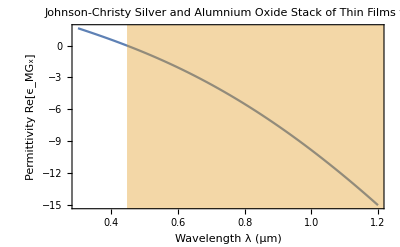

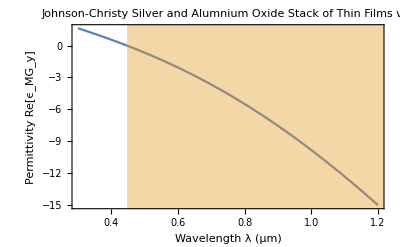

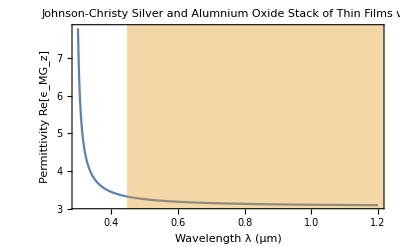

```mathematica
Subscript[v, x]=0;
Subscript[v, y]=0;
Subscript[v, z]=1;
f=10/46;

p0=λ/.Select[Solve[Subscript[ϵ, MG][Subscript[v, z],λ]==0,λ],Element[λ/.#1,Reals]&][[2]];

TypeII=Graphics[{Opacity[.4],RGBColor[0.880722, 0.611041, 0.142051],Rectangle[{FindRoot[Subscript[ϵ, MG][Subscript[v, x],h],{h,0}][[1,2]],-30},{3,30}]}];

Show[Plot[Re[Subscript[ϵ, MG][Subscript[v, x],λ]],{λ,.3,1.2},
PlotLabel->Style["Johnson-Christy Silver \n 
and Alumnium Oxide Stack of Thin Films ν_x",Bold],
Frame->{True,True,False,False},
FrameLabel->{"Wavelength λ (μm)","Permittivity Re[ϵ_MG_x]"}],
TypeII]

Show[Plot[Re[Subscript[ϵ, MG][Subscript[v, y],λ]],{λ,.3,1.2},
PlotLabel->Style["Johnson-Christy Silver \n 
and Alumnium Oxide Stack of Thin Films ν_y",Bold],
Frame->{True,True,False,False},
FrameLabel->{"Wavelength λ (μm)","Permittivity Re[ϵ_MG_y]"}],
TypeII]

Show[Plot[Re[Subscript[ϵ, MG][Subscript[v, z],λ]],{λ,.3,1.2},Exclusions->{p0},
ExclusionsStyle->Directive[Dotted,Gray],PlotRange->Full,
PlotLabel->Style["Johnson-Christy Silver \n 
and Alumnium Oxide Stack of Thin Films ν_z",Bold],
Frame->{True,True,False,False},
FrameLabel->{"Wavelength λ (μm)","Permittivity Re[ϵ_MG_z]"}],
TypeII]
```